# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\quantum_chaotic_channels\MG files\NEW DEFINITIONS

```mathematica
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\Chaometer.wl"]
```

```mathematica
?Reshuffle
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[haar];
haar[dim_Integer]:=Module[{l=2^dim,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
(*Define the Pauli matrices*)
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
(*Define collective spin operators for n spins*)
Clear[Jx,Jy,Jz];
Jx[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sx,IdentityMatrix[2]],{j,n}],{i,n}];
Jy[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sy,IdentityMatrix[2]],{j,n}],{i,n}];
Jz[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,n}],{i,n}];
(*Define the Lipkin Hamiltonian*)
Clear[Hlmg];
Hlmg[α_,gx_,gy_,n_]:=α*Jz[n]+(gx/(n-1))(Jx[n].Jx[n])+(gy/(n-1))(Jy[n].Jy[n]);
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Heisenberg with noise

```mathematica
Clear[Noisyheinsenberg];
Noisyheinsenberg[hz_,L_] := Module[{NNindices,a,b},
	NNindices=Normal[SparseArray[Thread[{#,#+1}->1],{L}]&/@Range[L-1]];
	a=N[Normal[Total[Join[(Pauli/@NNindices),(Pauli/@(2NNindices)),(Pauli/@(3NNindices))]]]];
	b=DiagonalMatrix[hz].Normal[Total[(Pauli[3#]&/@IdentityMatrix[L])]];
	a+b
]
```

# Mixed states

```mathematica
Clear[newsuper];
newsuper[t_,ψ0E_,eigVals_,eigVecs_,L_]:=Module[{ψf,ρfSE,basis=Table[VectorFromKetInComputationalBasis[i],{i,Tuples[{0,1},(L-1)]}]},ψf=Total[Table[Sqrt[ψ0E[[i]]]*StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[#],basis[[i]]],eigVals,eigVecs]&/@{{0},{1}},{i,Length[basis]}]];
ρfSE=Dyad[ψf[[#1]],ψf[[#2]]]&@@@Tuples[{1,2},2];Transpose[ Flatten[MatrixPartialTrace[#,2,{2,2^(L-1)}]]&/@ρfSE ]
]
```

```mathematica
L=5;
hx=1;
J=1;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ψe=ConstantArray[1/2^(L-1),2^(L-1)]
```

{1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16}

```mathematica
t=1;
superop=newsuper[t,ψe,eigenval,eigenvec,L];
```

```mathematica
Eigenvalues[superop]//Chop
```

{1.,-0.263616+0.313819 ⅈ,-0.263616-0.313819 ⅈ,0.258964}

```mathematica
Eigenvalues[Reshuffle[(1/2)superop]]
Eigenvalues[Reshuffle[(1/2)superop]]//Total
```

{0.586859,0.368088,0.0261938,0.0188591}

1.

```mathematica
tlist=Range[0,20,0.1];
```

```mathematica
data=Table[Transpose[{ConstantArray[t,4],Eigenvalues[Reshuffle[(1/2)newsuper[t,ψe,eigenval,eigenvec,L]]]}],{t,tlist}];
```

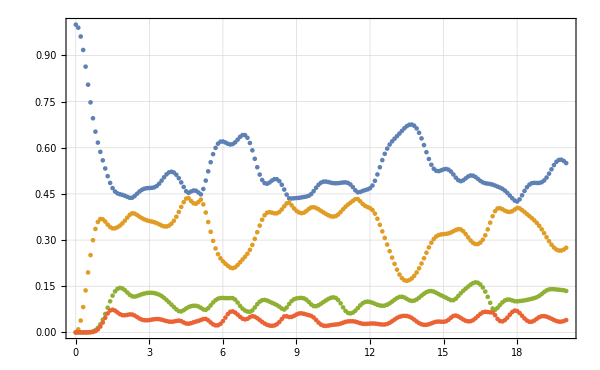

```mathematica
ListPlot[Transpose[data],PlotRange->All,ImageSize->600,PlotTheme->"Detailed"]
```

# Reshuffle

```mathematica
Clear[reshuf];
reshuf[matrix_,dimA_,dimB_]:=Module[{dims,reshuffled},dims={dimA,dimB};
ArrayReshape[Transpose[ArrayReshape[matrix,Join[dims,dims]],{1,3,2,4}],{dimA dimB,dimA dimB}]
];
```

```mathematica
Clear[reshape];
reshape[matrix_,dimA_,dimB_]:=ArrayFlatten[ArrayReshape[matrix,{dimA,dimB,dimA,dimB}]]
```

```mathematica
m=2;
n=2;
```

```mathematica
MatrixForm[A=Table[a[i,j],{i,4},{j,4}]]
```

(a[1,1] | a[1,2] | a[1,3] | a[1,4]
a[2,1] | a[2,2] | a[2,3] | a[2,4]
a[3,1] | a[3,2] | a[3,3] | a[3,4]
a[4,1] | a[4,2] | a[4,3] | a[4,4])

```mathematica
MatrixForm[choiA=reshape[A,2,2]]
```

(a[1,1] | a[1,2] | a[2,1] | a[2,2]
a[1,3] | a[1,4] | a[2,3] | a[2,4]
a[3,1] | a[3,2] | a[4,1] | a[4,2]
a[3,3] | a[3,4] | a[4,3] | a[4,4])

```mathematica
m=2;
n=4;
```

```mathematica
MatrixForm[A=Table[a[i,j],{i,m*n},{j,m*n}]]
```

(a[1,1] | a[1,2] | a[1,3] | a[1,4] | a[1,5] | a[1,6] | a[1,7] | a[1,8]
a[2,1] | a[2,2] | a[2,3] | a[2,4] | a[2,5] | a[2,6] | a[2,7] | a[2,8]
a[3,1] | a[3,2] | a[3,3] | a[3,4] | a[3,5] | a[3,6] | a[3,7] | a[3,8]
a[4,1] | a[4,2] | a[4,3] | a[4,4] | a[4,5] | a[4,6] | a[4,7] | a[4,8]
a[5,1] | a[5,2] | a[5,3] | a[5,4] | a[5,5] | a[5,6] | a[5,7] | a[5,8]
a[6,1] | a[6,2] | a[6,3] | a[6,4] | a[6,5] | a[6,6] | a[6,7] | a[6,8]
a[7,1] | a[7,2] | a[7,3] | a[7,4] | a[7,5] | a[7,6] | a[7,7] | a[7,8]
a[8,1] | a[8,2] | a[8,3] | a[8,4] | a[8,5] | a[8,6] | a[8,7] | a[8,8])

```mathematica
MatrixForm[choiA=reshape[A,m,n]]
```

(a[1,1] | a[1,2] | a[1,3] | a[1,4] | a[2,1] | a[2,2] | a[2,3] | a[2,4] | a[3,1] | a[3,2] | a[3,3] | a[3,4] | a[4,1] | a[4,2] | a[4,3] | a[4,4]
a[1,5] | a[1,6] | a[1,7] | a[1,8] | a[2,5] | a[2,6] | a[2,7] | a[2,8] | a[3,5] | a[3,6] | a[3,7] | a[3,8] | a[4,5] | a[4,6] | a[4,7] | a[4,8]
a[5,1] | a[5,2] | a[5,3] | a[5,4] | a[6,1] | a[6,2] | a[6,3] | a[6,4] | a[7,1] | a[7,2] | a[7,3] | a[7,4] | a[8,1] | a[8,2] | a[8,3] | a[8,4]
a[5,5] | a[5,6] | a[5,7] | a[5,8] | a[6,5] | a[6,6] | a[6,7] | a[6,8] | a[7,5] | a[7,6] | a[7,7] | a[7,8] | a[8,5] | a[8,6] | a[8,7] | a[8,8])

```mathematica
MatrixForm[ArrayFlatten[choiA=reshape[A,m,n]]]
```

(a[1,1] | a[1,2] | a[1,3] | a[1,4] | a[2,1] | a[2,2] | a[2,3] | a[2,4] | a[3,1] | a[3,2] | a[3,3] | a[3,4] | a[4,1] | a[4,2] | a[4,3] | a[4,4]
a[1,5] | a[1,6] | a[1,7] | a[1,8] | a[2,5] | a[2,6] | a[2,7] | a[2,8] | a[3,5] | a[3,6] | a[3,7] | a[3,8] | a[4,5] | a[4,6] | a[4,7] | a[4,8]
a[5,1] | a[5,2] | a[5,3] | a[5,4] | a[6,1] | a[6,2] | a[6,3] | a[6,4] | a[7,1] | a[7,2] | a[7,3] | a[7,4] | a[8,1] | a[8,2] | a[8,3] | a[8,4]
a[5,5] | a[5,6] | a[5,7] | a[5,8] | a[6,5] | a[6,6] | a[6,7] | a[6,8] | a[7,5] | a[7,6] | a[7,7] | a[7,8] | a[8,5] | a[8,6] | a[8,7] | a[8,8])

```mathematica
choiA//Dimensions
```

{4,16}

```mathematica
L=4;
J=hx=1;
hz=0.5;
```

```mathematica
H=IsingNNOpenHamiltonian[hx,hz,J,L];{eigenvals,eigenvecs}=Chop@Eigensystem[H];
t=10;
U=MatrixExp[- I*H*t];
SeedRandom[19242];
ψ=RandomChainProductState[L-1];
```

```mathematica
U//Dimensions
```

{16,16}

```mathematica
reshape[U,2,2^(L-1)]//Dimensions
```

{4,64}

```mathematica
AbsoluteTiming[MatrixForm[choi1=Chop[(1/2)*Reshuffle[Superoperator[t,ψ,eigenvals,eigenvecs,L]]]]]
```

{0.169091,(0.310707 | 0.00824121+0.0876287 ⅈ | 0.0787211+0.13548 ⅈ | 0.0664911-0.00188704 ⅈ
0.00824121-0.0876287 ⅈ | 0.273432 | 0.00406349+0.00122996 ⅈ | 0.131364+0.00337847 ⅈ
0.0787211-0.13548 ⅈ | 0.00406349-0.00122996 ⅈ | 0.189293 | -0.00824121-0.0876287 ⅈ
0.0664911+0.00188704 ⅈ | 0.131364-0.00337847 ⅈ | -0.00824121+0.0876287 ⅈ | 0.226568)}

```mathematica
AbsoluteTiming[MatrixForm[choi2=Chop[UR=reshape[U,2,2^(L-1)];UR.KroneckerProduct[SparseArray@IdentityMatrix[2^(L-1)]/2,Dyad[ψ]].ConjugateTranspose[UR]]]]
```

{0.0003543,(0.310707 | 0.00824121+0.0876287 ⅈ | 0.0787211+0.13548 ⅈ | 0.0664911-0.00188704 ⅈ
0.00824121-0.0876287 ⅈ | 0.273432 | 0.00406349+0.00122996 ⅈ | 0.131364+0.00337847 ⅈ
0.0787211-0.13548 ⅈ | 0.00406349-0.00122996 ⅈ | 0.189293 | -0.00824121-0.0876287 ⅈ
0.0664911+0.00188704 ⅈ | 0.131364-0.00337847 ⅈ | -0.00824121+0.0876287 ⅈ | 0.226568)}

```mathematica
choi1//Eigenvalues
choi2//Eigenvalues//Chop
```

{0.498077,0.34893,0.0914086,0.0615847}

{0.498077,0.34893,0.0914086,0.0615847}

```mathematica
superop=Reshuffle[2*choi1];
```

```mathematica
Eigenvalues[superop]//Chop
```

{1.,0.0999663+0.308921 ⅈ,0.0999663-0.308921 ⅈ,0.140582}

```mathematica
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[superop]]]];
```

```mathematica
eigenval//Chop
```

{0.0999663-0.308921 ⅈ,0.0999663+0.308921 ⅈ,0.140582,1.}

```mathematica
eigenvec[[-1]]
```

{0.651173+0. ⅈ,0.293637+0.205535 ⅈ,0.293637-0.205535 ⅈ,0.564835-2.77556×10^-16 ⅈ}

```mathematica
rho[{a,b,c,d}]
```

{{a,b},{c,d}}

```mathematica
rho[eigenvec[[-1]]]//MatrixForm
```

(0.651173+0. ⅈ | 0.293637+0.205535 ⅈ
0.293637-0.205535 ⅈ | 0.564835-2.77556×10^-16 ⅈ)

```mathematica
Eigenvalues[rho[eigenvec[[-1]]]]//Total
```

1.21601